```mathematica
Ms=480000; (*(*Saturation Magnetization*)*)
```

```mathematica
PK[x]:=PDF[LogNormalDistribution[Log[7000],0.3],x]; (*Αnisotropy Distribution*)
```

```mathematica
Kavg=Integrate[x*PK[x],{x,0,Infinity}](*Mean Anisotropy Value in σε J/m^3*)
```

7322.2

```mathematica
m0=1.25*10^-6; (*Magnetic Permeability of Vacuum*)
```

```mathematica
H0=24000; (*Applied Magnetic Field in A/m*)
```

```mathematica
Hk=(2*Kavg)/(m0*Ms)(*Anisotropy Field in A/m*)
```

24407.3

```mathematica
h=Function[x,x] (*Field Function*)
```

Function[x,x]

```mathematica
h[1] (*Test Value*)
```

1

```mathematica
Pd[x]:=PDF[LogNormalDistribution[Log[15*10^-9],0.25],x] (*Nanoparticle Size Distribution*)
```

```mathematica
dAvg = Integrate[x* Pd[x], {x, 0, Infinity}] (*Nanoparticle Volume Distribution in m*)
```

1.54762×10^-8

```mathematica
Vavg=(Pi/6) Integrate[x^3 *Pd[x],{x,0,Infinity}] (*Nanoparticle Volume Distribution*)
```

2.34109×10^-24

```mathematica
theta1=0Degree; (*First Energy Minimum Position*)
```

```mathematica
theta2=180Degree; (*Second Energy Minimum Position*)
```

```mathematica
theta3=90Degree; (*Energy Maximum Position*)
```

```mathematica
(*Mean and std deviation in radians*)phi0=Pi/6;(*30 degrees*)sigmaPhi=Pi/18;(*10 degrees*) 

Pphi[phi_]:=PDF[NormalDistribution[phi0,sigmaPhi],phi]/NIntegrate[PDF[NormalDistribution[phi0,sigmaPhi],u],{u,0,Pi}]; (*κατανομή γωνίας φ μεταξύ πεδίου και εύκολου άξονα*)
```

```mathematica
phiAvgCos[theta1]:=NIntegrate[Cos[theta1-phi] Pphi[phi],{phi,0,Pi}]; (*Mean Value of cos(θ1-φ)*)
```

```mathematica
phiAvgCos[theta2]:=NIntegrate[Cos[theta2-phi] Pphi[phi],{phi,0,Pi}];  (*Mean Value of cos(θ2-φ)*)
```

```mathematica
phiAvgCos[theta3]:=NIntegrate[Cos[theta3-phi] Pphi[phi],{phi,0,Pi}];   (*Mean Value of cos(θ3-φ)*)
```

```mathematica
Ep=Function[x,(Kavg*Vavg*Sin[theta3]^2-m0*h[x]*Vavg*Ms*phiAvgCos[theta3])-(Kavg*Vavg*Sin[theta1]^2-m0*h[x]*Vavg*Ms*phiAvgCos[theta1])] ;
(*Energy Barrier Between Maximum and First Energy Minimum ΔE=E3-E1 (Joule)*)
```

Function[x,(Kavg Vavg Sin[theta3]^2-m0 h[x] Vavg Ms phiAvgCos[theta3])-(Kavg Vavg Sin[theta1]^2-m0 h[x] Vavg Ms phiAvgCos[theta1])]

```mathematica
Em=Function[x,(Kavg*Vavg*Sin[theta3]^2-m0*h[x]*Vavg*Ms*phiAvgCos[theta3])-(Kavg*Vavg*Sin[theta2]^2-m0*h[x]*Vavg*Ms*phiAvgCos[theta2])]; 
(*Energy Barrier Between Maximum and Second Energy Minimum ΔE=E3-E2 (Joule)*)
```

Function[x,(Kavg Vavg Sin[theta3]^2-m0 h[x] Vavg Ms phiAvgCos[theta3])-(Kavg Vavg Sin[theta2]^2-m0 h[x] Vavg Ms phiAvgCos[theta2])]

```mathematica
T=300; (*Temperature in Kelvin*)
```

300

```mathematica
kB=1.38*10^-23; (*Boltzmann Constant*)
```

1.38×10^-23

```mathematica
n0=10^9; (*Συχνότητα Larmor σε Hz*)
```

1000000000

```mathematica
f=765000; (*Field Frequency in Hz*)
```

765000

```mathematica
n1=Function[x,n0*Exp[-Em[x]/(kB*T)]]; (*Transition Probability Rate from θ1 to θ2 in Hz*)
```

Function[x,n0 Exp[-Em[x]/(kB T)]]

Function[x,n0 Exp[-Em[x]/(k T)]]

```mathematica
n2=Function[x,n0*Exp[-Ep[x]/(kB*T)]]; (*Transition Probability Rate from θ2 to θ1 in Hz*)
```

Function[x,n0 Exp[-Ep[x]/(kB T)]]

```mathematica
s1=NDSolve[{y'[x]==(2*Ms*(n1[x]-((n1[x]+n2[x])/2)*((y[x]/Ms)+1)))/(4*f*H0),y[0]==0},y,{x,0,H0}] 
(*Solution of the Magnetization Differential Equation*)
```

{{y→InterpolatingFunction[…]}}

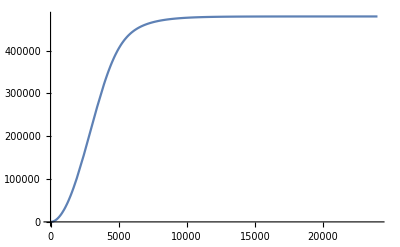

```mathematica
P1=Plot[Evaluate[y[x]/.s1],{x,0,H0},PlotRange->All]
```

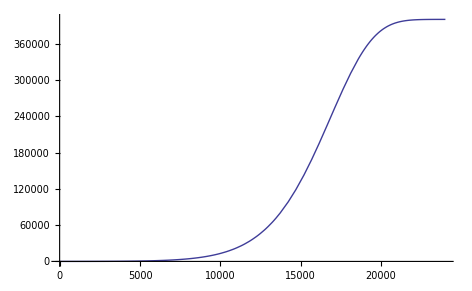

```mathematica
s2=NDSolve[{y'[x]==(2*Ms*(n1[x]-((n1[x]+n2[x])/2)*((y[x]/Ms)+1)))/(-4*f*H0),y[H0]==Ms},y,{x,-H0,H0}]
```

{{y→InterpolatingFunction[…]}}

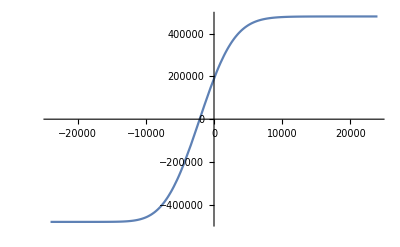

```mathematica
P2=Plot[Evaluate[y[x]/.s2],{x,-H0,H0},PlotRange->All]
```

```mathematica
s3=NDSolve[{y'[x]==(2*Ms*(n1[x]-((n1[x]+n2[x])/2)*((y[x]/Ms)+1)))/(4*f*H0),y[-H0]==-Ms},y,{x,-H0,H0}]
```

{{y→InterpolatingFunction[…]}}

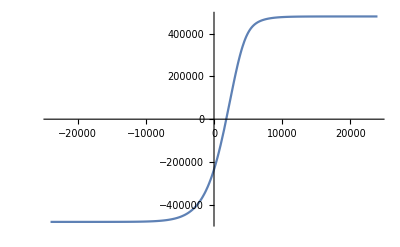

```mathematica
P3=Plot[Evaluate[y[x]/.s3],{x,-H0,H0},PlotRange->All]
```

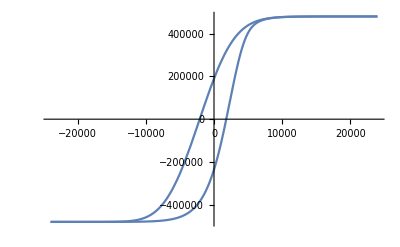

```mathematica
Show[P3,P2]
```

```mathematica
mydatapoints=Cases[Show[P3,P2],Line[{x__}]->x,Infinity]
```

{{-24000.,-400000.},{-23985.3,-400000.},{-23970.6,-400000.},{-23941.1,-400000.},{-23926.4,-400000.},«1563»,{23934.1,400000.},{23950.6,400000.},{23967.1,400000.},{23983.5,400000.},{24000.,400000.}}

```mathematica
Grid[mydatapoints]
```

-24000. | -400000.
-23985.3 | -400000.
-23970.6 | -400000.
-23941.1 | -400000.
-23926.4 | -400000.
-23911.7 | -400000.
-23882.2 | -400000.
-23867.5 | -400000.
-23852.8 | -400000.
-23823.3 | -400000.
-23764.5 | -400000.
-23749.7 | -400000.
-23735. | -400000.
-23705.6 | -400000.
-23646.7 | -400000.
-23632. | -400000.
-23617.2 | -400000.
-23587.8 | -400000.
-23528.9 | -400000.
-23514.2 | -400000.
-23499.5 | -400000.
-23470. | -400000.
-23411.1 | -400000.
-23293.4 | -400000.
-23057.8 | -400000.
-23041.9 | -400000.
-23025.9 | -400000.
-22994. | -400000.
-22930.1 | -400000.
-22802.5 | -400000.
-22786.5 | -400000.
-22770.5 | -400000.
-22738.6 | -400000.
-22674.8 | -400000.
-22547.1 | -400000.
-22531.2 | -400000.
-22515.2 | -400000.
-22483.3 | -400000.
-22419.4 | -400000.
-22291.8 | -400000.
-22275.8 | -400000.
-22259.8 | -400000.
-22227.9 | -400000.
-22164.1 | -400000.
-22036.4 | -400000.
-22021.5 | -400000.
-22006.6 | -400000.
-21976.8 | -400000.
-21917.2 | -400000.
-21798. | -400000.
-21783.1 | -400000.
-21768.2 | -400000.
-21738.4 | -400000.
-21678.7 | -400000.
-21559.5 | -400000.
-21544.6 | -400000.
-21529.7 | -400000.
-21499.9 | -400000.
-21440.3 | -400000.
-21321.1 | -400000.
-21082.7 | -400000.
-21068.1 | -400000.
-21053.4 | -400000.
-21024.2 | -400000.
-20965.8 | -400000.
-20848.9 | -400000.
-20834.3 | -400000.
-20819.7 | -400000.
-20790.5 | -400000.
-20732. | -400000.
-20615.1 | -400000.
-20600.5 | -400000.
-20585.9 | -400000.
-20556.7 | -400000.
-20498.3 | -400000.
-20381.4 | -400000.
-20147.6 | -400000.
-20131.8 | -400000.
-20115.9 | -400000.
-20084.2 | -400000.
-20020.8 | -400000.
-19894.1 | -400000.
-19878.2 | -400000.
-19862.4 | -400000.
-19830.7 | -400000.
-19767.3 | -400000.
-19640.5 | -400000.
-19624.6 | -400000.
-19608.8 | -400000.
-19577.1 | -400000.
-19513.7 | -400000.
-19386.9 | -400000.
-19133.4 | -400000.
-19118.6 | -400000.
-19103.8 | -400000.
-19074.2 | -400000.
-19015. | -400000.
-18896.7 | -399999.
-18881.9 | -399999.
-18867.1 | -399999.
-18837.5 | -399999.
-18778.4 | -399999.
-18660.1 | -399999.
-18645.3 | -399999.
-18630.5 | -399999.
-18600.9 | -399999.
-18541.7 | -399999.
-18423.4 | -399999.
-18186.8 | -399999.
-18170.7 | -399999.
-18154.7 | -399999.
-18122.6 | -399999.
-18058.5 | -399999.
-17930.3 | -399999.
-17914.3 | -399999.
-17898.2 | -399999.
-17866.2 | -399999.
-17802.1 | -399999.
-17673.8 | -399999.
-17657.8 | -399999.
-17641.8 | -399999.
-17609.7 | -399999.
-17545.6 | -399999.
-17417.4 | -399999.
-17160.9 | -399998.
-17145.2 | -399998.
-17129.4 | -399998.
-17098. | -399998.
-17035. | -399998.
-16909.1 | -399998.
-16893.4 | -399998.
-16877.7 | -399998.
-16846.2 | -399998.
-16783.2 | -399998.
-16657.4 | -399998.
-16641.6 | -399998.
-16625.9 | -399998.
-16594.4 | -399998.
-16531.5 | -399997.
-16405.6 | -399997.
-16153.8 | -399997.
-16139.1 | -399997.
-16124.4 | -399997.
-16095.1 | -399997.
-16036.4 | -399997.
-15918.9 | -399996.
-15904.2 | -399996.
-15889.6 | -399996.
-15860.2 | -399996.
-15801.5 | -399996.
-15684.1 | -399996.
-15669.4 | -399996.
-15654.7 | -399996.
-15625.3 | -399995.
-15566.6 | -399995.
-15449.2 | -399995.
-15214.3 | -399994.
-15198.4 | -399994.
-15182.5 | -399994.
-15150.7 | -399994.
-15087. | -399994.
-14959.7 | -399993.
-14943.8 | -399993.
-14927.8 | -399993.
-14896. | -399993.
-14832.3 | -399992.
-14705. | -399992.
-14689.1 | -399992.
-14673.2 | -399992.
-14641.3 | -399991.
-14577.7 | -399991.
-14450.3 | -399990.
-14195.6 | -399989.
-14180.8 | -399989.
-14165.9 | -399988.
-14136.2 | -399988.
-14076.8 | -399988.
-13957.9 | -399987.
-13943. | -399987.
-13928.2 | -399987.
-13898.5 | -399986.
-13839. | -399986.
-13720.1 | -399985.
-13705.3 | -399985.
-13690.4 | -399984.
-13660.7 | -399984.
-13601.3 | -399984.
-13482.4 | -399982.
-13244.6 | -399979.
-13230.1 | -399979.
-13215.5 | -399979.
-13186.4 | -399979.
-13128.1 | -399978.
-13011.6 | -399976.
-12997. | -399976.
-12982.4 | -399976.
-12953.3 | -399975.
-12895. | -399975.
-12778.5 | -399973.
-12763.9 | -399972.
-12749.4 | -399972.
-12720.2 | -399972.
-12662. | -399971.
-12545.4 | -399969.
-12312.3 | -399964.
-12296.5 | -399963.
-12280.7 | -399963.
-12249.1 | -399962.
-12185.9 | -399961.
-12059.5 | -399958.
-12043.6 | -399957.
-12027.8 | -399957.
-11996.2 | -399956.
-11933. | -399955.
-11806.6 | -399951.
-11790.8 | -399951.
-11775. | -399950.
-11743.3 | -399949.
-11680.1 | -399947.
-11553.7 | -399943.
-11300.8 | -399934.
-11286. | -399933.
-11271.3 | -399933.
-11241.8 | -399932.
-11182.8 | -399929.
-11064.8 | -399924.
-11050.1 | -399924.
-11035.3 | -399923.
-11005.8 | -399922.
-10946.8 | -399919.
-10828.9 | -399913.
-10814.1 | -399913.
-10799.4 | -399912.
-10769.9 | -399910.
-10710.9 | -399907.
-10592.9 | -399901.
-10356.9 | -399886.
-10340.9 | -399885.
-10325. | -399884.
-10293. | -399882.
-10229. | -399878.
-10101.1 | -399869.
-10085.2 | -399868.
-10069.2 | -399866.
-10037.2 | -399864.
-9973.26 | -399859.
-9845.37 | -399849.
-9829.39 | -399847.
-9813.4 | -399846.
-9781.43 | -399843.
-9717.48 | -399837.
-9589.59 | -399826.
-9333.82 | -399799.
-9318.12 | -399797.
-9302.43 | -399796.
-9271.04 | -399792.
-9208.26 | -399785.
-9082.71 | -399770.
-9067.02 | -399768.
-9051.33 | -399766.
-9019.94 | -399762.
-8957.16 | -399753.
-8831.61 | -399736.
-8815.92 | -399734.
-8800.23 | -399732.
-8768.84 | -399727.
-8706.06 | -399718.
-8580.51 | -399698.
-8329.41 | -399655.
-8314.78 | -399652.
-8300.14 | -399649.
-8270.87 | -399644.
-8212.32 | -399633.
-8095.23 | -399609.
-7861.05 | -399558.
-7846.42 | -399555.
-7831.78 | -399551.
-7802.51 | -399544.
-7743.96 | -399530.
-7626.87 | -399501.
-7392.7 | -399437.
-7376.82 | -399432.
-7360.95 | -399427.
-7329.2 | -399418.
-7265.7 | -399399.
-7138.7 | -399358.
-7122.83 | -399353.
-7106.96 | -399348.
-7075.21 | -399337.
-7011.71 | -399316.
-6884.71 | -399270.
-6868.84 | -399264.
-6852.96 | -399258.
-6821.21 | -399246.
-6757.72 | -399222.
-6630.72 | -399171.
-6376.73 | -399058.
-6361.91 | -399051.
-6347.1 | -399044.
-6317.46 | -399030.
-6258.19 | -399001.
-6139.66 | -398941.
-5902.59 | -398811.
-5887.77 | -398802.
-5872.96 | -398793.
-5843.32 | -398776.
-5784.06 | -398740.
-5665.52 | -398665.
-5428.45 | -398503.
-5412.4 | -398491.
-5396.34 | -398480.
-5364.23 | -398456.
-5300.01 | -398408.
-5171.57 | -398307.
-4914.69 | -398087.
-4898.63 | -398073.
-4882.58 | -398058.
-4850.47 | -398028.
-4786.25 | -397968.
-4657.8 | -397841.
-4400.92 | -397566.
-4385.16 | -397549.
-4369.4 | -397531.
-4337.87 | -397494.
-4274.82 | -397420.
-4148.72 | -397265.
-3896.51 | -396930.
-3880.75 | -396908.
-3864.99 | -396885.
-3833.46 | -396840.
-3770.41 | -396748.
-3644.31 | -396556.
-3392.1 | -396141.
-3377.4 | -396116.
-3362.69 | -396090.
-3333.28 | -396038.
-3274.46 | -395932.
-3156.82 | -395713.
-2921.54 | -395241.
-2906.83 | -395210.
-2892.13 | -395179.
-2862.72 | -395116.
-2803.89 | -394987.
-2686.25 | -394721.
-2450.97 | -394149.
-2435.03 | -394109.
-2419.08 | -394068.
-2387.2 | -393985.
-2323.42 | -393816.
-2195.87 | -393465.
-1940.78 | -392708.
-1924.83 | -392658.
-1908.89 | -392607.
-1877. | -392506.
-1813.23 | -392299.
-1685.68 | -391870.
-1430.59 | -390944.
-1415.7 | -390887.
-1400.82 | -390830.
-1371.04 | -390715.
-1311.5 | -390480.
-1192.41 | -389993.
-954.24 | -388951.
-939.354 | -388883.
-924.468 | -388814.
-894.696 | -388675.
-835.153 | -388393.
-716.066 | -387810.
-477.892 | -386561.
-463.299 | -386481.
-448.705 | -386400.
-419.518 | -386238.
-361.144 | -385907.
-244.396 | -385224.
-10.8992 | -383766.
3.69431 | -383671.
18.2878 | -383575.
47.4749 | -383382.
105.849 | -382989.
222.597 | -382178.
456.094 | -380448.
471.926 | -380325.
487.757 | -380202.
519.421 | -379953.
582.748 | -379447.
709.403 | -378399.
962.712 | -376157.
978.544 | -376010.
994.376 | -375862.
1026.04 | -375564.
1089.37 | -374958.
1216.02 | -373705.
1469.33 | -371025.
1484.1 | -370862.
1498.88 | -370697.
1528.43 | -370366.
1587.52 | -369693.
1705.72 | -368305.
1942.1 | -365355.
1956.88 | -365163.
1971.65 | -364970.
2001.2 | -364580.
2060.3 | -363790.
2178.49 | -362161.
2414.88 | -358704.
2430.89 | -358460.
2446.9 | -358215.
2478.93 | -357720.
2542.98 | -356715.
2671.08 | -354641.
2927.28 | -350224.
2943.29 | -349936.
2959.3 | -349646.
2991.33 | -349062.
3055.38 | -347876.
3183.48 | -345430.
3439.68 | -340231.
3455.4 | -339898.
3471.12 | -339564.
3502.56 | -338890.
3565.44 | -337523.
3691.2 | -334709.
3942.72 | -328745.
3958.44 | -328357.
3974.16 | -327967.
4005.6 | -327182.
4068.49 | -325589.
4194.25 | -322312.
4445.77 | -315384.
4460.43 | -314965.
4475.09 | -314543.
4504.42 | -313695.
4563.07 | -311976.
4680.37 | -308452.
4914.97 | -301041.
4929.63 | -300562.
4944.3 | -300080.
4973.62 | -299112.
5032.27 | -297150.
5149.57 | -293131.
5384.17 | -284699.
5400.07 | -284108.
5415.97 | -283515.
5447.78 | -282321.
5511.38 | -279902.
5638.59 | -274941.
5893. | -264517.
6401.83 | -241581.
6416.67 | -240868.
6431.51 | -240154.
6461.2 | -238717.
6520.57 | -235813.
6639.32 | -229883.
6876.81 | -217536.
7351.79 | -190851.
7366.34 | -189991.
7380.89 | -189129.
7409.99 | -187397.
7468.2 | -183902.
7584.6 | -176792.
7817.42 | -162091.
8283.05 | -130786.
9293.55 | -54757.6
10236.4 | 23989.
11258.4 | 112954.
12212.8 | 193114.
12227.4 | 194285.
12242.1 | 195453.
12271.3 | 197782.
12329.8 | 202412.
12446.7 | 211555.
12680.7 | 229331.
12695.3 | 230418.
12709.9 | 231502.
12739.1 | 233661.
12797.6 | 237943.
12914.6 | 246357.
13148.5 | 262556.
13164.4 | 263622.
13180.2 | 264685.
13211.9 | 266797.
13275.4 | 270972.
13402.2 | 279115.
13656. | 294551.
13671.8 | 295478.
13687.7 | 296399.
13719.4 | 298228.
13782.8 | 301831.
13909.7 | 308812.
14163.4 | 321862.
14178.2 | 322586.
14193. | 323305.
14222.6 | 324731.
14281.8 | 327532.
14400.2 | 332935.
14637. | 342943.
14651.8 | 343533.
14666.6 | 344120.
14696.2 | 345280.
14755.4 | 347552.
14873.8 | 351902.
15110.7 | 359842.
15126.7 | 360344.
15142.7 | 360842.
15174.8 | 361824.
15239. | 363734.
15367.3 | 367348.
15383.3 | 367781.
15399.4 | 368209.
15431.4 | 369054.
15495.6 | 370693.
15623.9 | 373779.
15639.9 | 374147.
15656. | 374511.
15688.1 | 375228.
15752.2 | 376616.
15880.5 | 379216.
15896.6 | 379524.
15912.6 | 379830.
15944.7 | 380430.
16008.8 | 381589.
16137.1 | 383748.
16152.9 | 383999.
16168.6 | 384247.
16200.1 | 384733.
16263.1 | 385671.
16389.1 | 387411.
16404.8 | 387616.
16420.6 | 387819.
16452.1 | 388216.
16515.1 | 388980.
16641. | 390388.
16656.8 | 390553.
16672.5 | 390716.
16704. | 391036.
16767. | 391648.
16782.8 | 391795.
16798.5 | 391941.
16830. | 392226.
16893. | 392770.
16908.7 | 392902.
16924.5 | 393031.
16956. | 393284.
17018.9 | 393766.
17144.9 | 394647.
17159.6 | 394742.
17174.3 | 394837.
17203.7 | 395021.
17262.4 | 395373.
17277.1 | 395457.
17291.8 | 395541.
17321.2 | 395704.
17379.9 | 396015.
17394.6 | 396089.
17409.3 | 396163.
17438.7 | 396307.
17497.5 | 396580.
17615. | 397077.
17629.7 | 397134.
17644.3 | 397191.
17673.7 | 397301.
17732.5 | 397511.
17747.2 | 397561.
17761.9 | 397610.
17791.2 | 397706.
17850. | 397888.
17864.7 | 397932.
17879.4 | 397975.
17908.7 | 398058.
17967.5 | 398216.
18085. | 398499.
18100.9 | 398534.
18116.9 | 398568.
18148.7 | 398635.
18212.4 | 398761.
18228.4 | 398791.
18244.3 | 398820.
18276.1 | 398876.
18339.8 | 398982.
18355.8 | 399007.
18371.7 | 399032.
18403.6 | 399079.
18467.3 | 399168.
18483.2 | 399189.
18499.1 | 399210.
18531. | 399250.
18594.7 | 399324.
18610.6 | 399341.
18626.5 | 399358.
18658.4 | 399391.
18722.1 | 399453.
18738. | 399468.
18754. | 399482.
18785.8 | 399509.
18849.5 | 399560.
18865.4 | 399572.
18881.4 | 399584.
18913.2 | 399606.
18976.9 | 399648.
18992.9 | 399658.
19008.8 | 399667.
19040.6 | 399686.
19104.4 | 399720.
19119.2 | 399727.
19134.1 | 399735.
19163.8 | 399749.
19223.3 | 399775.
19238.2 | 399781.
19253. | 399787.
19282.8 | 399799.
19342.3 | 399820.
19357.1 | 399825.
19372. | 399830.
19401.7 | 399839.
19461.2 | 399857.
19476.1 | 399861.
19491. | 399865.
19520.7 | 399872.
19580.2 | 399887.
19595. | 399890.
19609.9 | 399893.
19639.7 | 399899.
19699.1 | 399911.
19714. | 399913.
19728.9 | 399916.
19758.6 | 399921.
19818.1 | 399930.
19833. | 399932.
19847.8 | 399934.
19877.6 | 399938.
19937. | 399945.
19951.9 | 399947.
19966.8 | 399949.
19996.5 | 399952.
20056. | 399958.
20070.6 | 399959.
20085.2 | 399960.
20114.3 | 399963.
20172.6 | 399967.
20187.2 | 399968.
20201.8 | 399969.
20230.9 | 399971.
20289.2 | 399975.
20303.8 | 399976.
20318.4 | 399976.
20347.5 | 399978.
20362.1 | 399979.
20376.7 | 399979.
20405.9 | 399981.
20420.4 | 399981.
20435. | 399982.
20464.2 | 399983.
20522.5 | 399985.
20537.1 | 399986.
20551.6 | 399986.
20580.8 | 399987.
20595.4 | 399988.
20609.9 | 399988.
20639.1 | 399989.
20653.7 | 399989.
20668.2 | 399989.
20697.4 | 399990.
20755.7 | 399991.
20770.3 | 399992.
20784.9 | 399992.
20814. | 399993.
20828.6 | 399993.
20843.2 | 399993.
20872.3 | 399994.
20886.9 | 399994.
20901.5 | 399994.
20930.6 | 399994.
20988.9 | 399995.
21004.8 | 399995.
21020.6 | 399996.
21052.2 | 399996.
21068. | 399996.
21083.8 | 399996.
21115.5 | 399997.
21131.3 | 399997.
21147.1 | 399997.
21178.7 | 399997.
21242. | 399997.
21257.8 | 399998.
21273.6 | 399998.
21305.3 | 399998.
21321.1 | 399998.
21336.9 | 399998.
21368.5 | 399998.
21384.3 | 399998.
21400.2 | 399998.
21431.8 | 399998.
21495. | 399999.
21510.9 | 399999.
21526.7 | 399999.
21558.3 | 399999.
21574.1 | 399999.
21589.9 | 399999.
21621.6 | 399999.
21637.4 | 399999.
21653.2 | 399999.
21684.8 | 399999.
21748.1 | 399999.
21763.9 | 399999.
21779.7 | 399999.
21811.4 | 399999.
21827.2 | 399999.
21843. | 399999.
21874.6 | 400000.
21890.4 | 400000.
21906.2 | 400000.
21937.9 | 400000.
22001.1 | 400000.
22015.9 | 400000.
22030.7 | 400000.
22060.2 | 400000.
22074.9 | 400000.
22089.7 | 400000.
22119.2 | 400000.
22134. | 400000.
22148.7 | 400000.
22178.2 | 400000.
22237.3 | 400000.
22252. | 400000.
22266.8 | 400000.
22296.3 | 400000.
22311.1 | 400000.
22325.8 | 400000.
22355.3 | 400000.
22370.1 | 400000.
22384.8 | 400000.
22414.4 | 400000.
22473.4 | 400000.
22488.2 | 400000.
22502.9 | 400000.
22532.4 | 400000.
22547.2 | 400000.
22561.9 | 400000.
22591.5 | 400000.
22606.2 | 400000.
22621. | 400000.
22650.5 | 400000.
22709.5 | 400000.
22724.3 | 400000.
22739. | 400000.
22768.6 | 400000.
22783.3 | 400000.
22798.1 | 400000.
22827.6 | 400000.
22842.3 | 400000.
22857.1 | 400000.
22886.6 | 400000.
22945.6 | 400000.
22962.1 | 400000.
22978.6 | 400000.
23011.5 | 400000.
23028. | 400000.
23044.5 | 400000.
23077.4 | 400000.
23093.9 | 400000.
23110.4 | 400000.
23143.3 | 400000.
23209.2 | 400000.
23225.7 | 400000.
23242.2 | 400000.
23275.1 | 400000.
23341. | 400000.
23357.5 | 400000.
23374. | 400000.
23406.9 | 400000.
23472.8 | 400000.
23489.3 | 400000.
23505.8 | 400000.
23538.7 | 400000.
23604.6 | 400000.
23621.1 | 400000.
23637.6 | 400000.
23670.5 | 400000.
23736.4 | 400000.
23752.9 | 400000.
23769.4 | 400000.
23802.3 | 400000.
23868.2 | 400000.
23884.7 | 400000.
23901.2 | 400000.
23934.1 | 400000.
23950.6 | 400000.
23967.1 | 400000.
23983.5 | 400000.
24000. | 400000.
-24000. | -400000.
-23985.3 | -400000.
-23970.6 | -400000.
-23941.1 | -400000.
-23882.2 | -400000.
-23867.5 | -400000.
-23852.8 | -400000.
-23823.3 | -400000.
-23764.5 | -400000.
-23749.7 | -400000.
-23735. | -400000.
-23705.6 | -400000.
-23646.7 | -400000.
-23528.9 | -400000.
-23514.2 | -400000.
-23499.5 | -400000.
-23470. | -400000.
-23411.1 | -400000.
-23396.4 | -400000.
-23381.7 | -400000.
-23352.3 | -400000.
-23293.4 | -400000.
-23278.6 | -400000.
-23263.9 | -400000.
-23234.5 | -400000.
-23175.6 | -400000.
-23160.9 | -400000.
-23146.2 | -400000.
-23116.7 | -400000.
-23057.8 | -400000.
-23041.9 | -400000.
-23025.9 | -400000.
-22994. | -400000.
-22978. | -400000.
-22962.1 | -400000.
-22930.1 | -400000.
-22914.2 | -400000.
-22898.2 | -400000.
-22866.3 | -400000.
-22802.5 | -400000.
-22786.5 | -400000.
-22770.5 | -400000.
-22738.6 | -400000.
-22722.7 | -400000.
-22706.7 | -400000.
-22674.8 | -400000.
-22658.8 | -400000.
-22642.9 | -400000.
-22611. | -400000.
-22547.1 | -400000.
-22531.2 | -400000.
-22515.2 | -400000.
-22483.3 | -400000.
-22467.3 | -400000.
-22451.4 | -400000.
-22419.4 | -400000.
-22403.5 | -400000.
-22387.5 | -400000.
-22355.6 | -400000.
-22291.8 | -400000.
-22275.8 | -400000.
-22259.8 | -400000.
-22227.9 | -400000.
-22212. | -400000.
-22196. | -400000.
-22164.1 | -400000.
-22148.1 | -400000.
-22132.2 | -400000.
-22100.2 | -400000.
-22036.4 | -400000.
-22021.5 | -400000.
-22006.6 | -400000.
-21976.8 | -400000.
-21961.9 | -400000.
-21947. | -400000.
-21917.2 | -400000.
-21902.3 | -400000.
-21887.4 | -400000.
-21857.6 | -399999.
-21798. | -399999.
-21783.1 | -399999.
-21768.2 | -399999.
-21738.4 | -399999.
-21723.5 | -399999.
-21708.6 | -399999.
-21678.7 | -399999.
-21663.8 | -399999.
-21648.9 | -399999.
-21619.1 | -399999.
-21559.5 | -399999.
-21544.6 | -399999.
-21529.7 | -399999.
-21499.9 | -399999.
-21485. | -399999.
-21470.1 | -399999.
-21440.3 | -399998.
-21425.4 | -399998.
-21410.5 | -399998.
-21380.7 | -399998.
-21321.1 | -399998.
-21306.2 | -399998.
-21291.3 | -399998.
-21261.5 | -399998.
-21246.6 | -399997.
-21231.7 | -399997.
-21201.9 | -399997.
-21187. | -399997.
-21172.1 | -399997.
-21142.3 | -399997.
-21082.7 | -399996.
-21068.1 | -399996.
-21053.4 | -399996.
-21024.2 | -399996.
-21009.6 | -399995.
-20995. | -399995.
-20965.8 | -399995.
-20951.2 | -399995.
-20936.6 | -399995.
-20907.3 | -399994.
-20848.9 | -399993.
-20834.3 | -399993.
-20819.7 | -399993.
-20790.5 | -399992.
-20775.9 | -399992.
-20761.2 | -399992.
-20732. | -399991.
-20717.4 | -399991.
-20702.8 | -399990.
-20673.6 | -399990.
-20615.1 | -399988.
-20600.5 | -399988.
-20585.9 | -399987.
-20556.7 | -399986.
-20542.1 | -399986.
-20527.5 | -399985.
-20498.3 | -399984.
-20483.7 | -399984.
-20469. | -399983.
-20439.8 | -399982.
-20381.4 | -399979.
-20366.8 | -399979.
-20352.2 | -399978.
-20323. | -399977.
-20308.3 | -399976.
-20293.7 | -399975.
-20264.5 | -399973.
-20249.9 | -399972.
-20235.3 | -399971.
-20206.1 | -399970.
-20147.6 | -399965.
-20131.8 | -399964.
-20115.9 | -399963.
-20084.2 | -399960.
-20068.4 | -399959.
-20052.5 | -399957.
-20020.8 | -399954.
-20005. | -399953.
-19989.2 | -399951.
-19957.5 | -399948.
-19894.1 | -399940.
-19878.2 | -399938.
-19862.4 | -399936.
-19830.7 | -399932.
-19814.8 | -399929.
-19799. | -399927.
-19767.3 | -399922.
-19751.4 | -399920.
-19735.6 | -399917.
-19703.9 | -399911.
-19640.5 | -399899.
-19624.6 | -399896.
-19608.8 | -399893.
-19577.1 | -399886.
-19513.7 | -399871.
-19497.9 | -399867.
-19482. | -399862.
-19450.3 | -399854.
-19386.9 | -399835.
-19371.1 | -399830.
-19355.2 | -399824.
-19323.5 | -399813.
-19260.1 | -399790.
-19244.3 | -399783.
-19228.4 | -399777.
-19196.7 | -399763.
-19133.4 | -399734.
-19118.6 | -399727.
-19103.8 | -399720.
-19074.2 | -399704.
-19015. | -399671.
-19000.2 | -399662.
-18985.4 | -399653.
-18955.9 | -399635.
-18896.7 | -399595.
-18881.9 | -399584.
-18867.1 | -399573.
-18837.5 | -399551.
-18778.4 | -399503.
-18763.6 | -399490.
-18748.8 | -399477.
-18719.2 | -399450.
-18660.1 | -399393.
-18645.3 | -399378.
-18630.5 | -399363.
-18600.9 | -399331.
-18541.7 | -399263.
-18526.9 | -399245.
-18512.2 | -399226.
-18482.6 | -399188.
-18423.4 | -399108.
-18408.6 | -399087.
-18393.8 | -399065.
-18364.2 | -399020.
-18305.1 | -398926.
-18186.8 | -398711.
-18170.7 | -398680.
-18154.7 | -398647.
-18122.6 | -398581.
-18058.5 | -398439.
-18042.5 | -398401.
-18026.5 | -398363.
-17994.4 | -398284.
-17930.3 | -398117.
-17914.3 | -398073.
-17898.2 | -398029.
-17866.2 | -397936.
-17802.1 | -397741.
-17673.8 | -397301.
-17657.8 | -397242.
-17641.8 | -397181.
-17609.7 | -397056.
-17545.6 | -396792.
-17529.6 | -396723.
-17513.6 | -396652.
-17481.5 | -396508.
-17417.4 | -396203.
-17401.4 | -396123.
-17385.3 | -396042.
-17353.3 | -395876.
-17289.2 | -395526.
-17160.9 | -394751.
-17145.2 | -394649.
-17129.4 | -394545.
-17098. | -394332.
-17035. | -393885.
-17019.3 | -393769.
-17003.6 | -393651.
-16972.1 | -393410.
-16909.1 | -392905.
-16893.4 | -392774.
-16877.7 | -392641.
-16846.2 | -392369.
-16783.2 | -391800.
-16657.4 | -390559.
-16641.6 | -390394.
-16625.9 | -390227.
-16594.4 | -389885.
-16531.5 | -389172.
-16405.6 | -387626.
-16389.8 | -387421.
-16374.1 | -387213.
-16342.6 | -386790.
-16279.7 | -385910.
-16153.8 | -384013.
-16139.1 | -383780.
-16124.4 | -383543.
-16095.1 | -383063.
-16036.4 | -382070.
-15918.9 | -379949.
-15904.2 | -379671.
-15889.6 | -379390.
-15860.2 | -378819.
-15801.5 | -377642.
-15684.1 | -375140.
-15669.4 | -374813.
-15654.7 | -374482.
-15625.3 | -373812.
-15566.6 | -372433.
-15449.2 | -369514.
-15214.3 | -363009.
-15198.4 | -362535.
-15182.5 | -362057.
-15150.7 | -361086.
-15087. | -359094.
-14959.7 | -354895.
-14943.8 | -354350.
-14927.8 | -353800.
-14896. | -352687.
-14832.3 | -350406.
-14705. | -345620.
-14689.1 | -345001.
-14673.2 | -344376.
-14641.3 | -343114.
-14577.7 | -340533.
-14450.3 | -335141.
-14195.6 | -323432.
-14180.8 | -322710.
-14165.9 | -321985.
-14136.2 | -320521.
-14076.8 | -317543.
-13957.9 | -311385.
-13720.1 | -298271.
-13244.6 | -268958.
-13230.1 | -267998.
-13215.5 | -267034.
-13186.4 | -265096.
-13128.1 | -261178.
-13011.6 | -253177.
-12778.5 | -236547.
-12312.3 | -201035.
-11300.8 | -116622.
-10356.9 | -34405.5
-9333.82 | 51524.8
-8329.41 | 127533.
-8314.78 | 128563.
-8300.14 | 129590.
-8270.87 | 131637.
-8212.32 | 135701.
-8095.23 | 143714.
-7861.05 | 159264.
-7392.7 | 188427.
-7376.82 | 189370.
-7360.95 | 190310.
-7329.2 | 192181.
-7265.7 | 195886.
-7138.7 | 203153.
-6884.71 | 217113.
-6376.73 | 242779.
-6361.91 | 243483.
-6347.1 | 244185.
-6317.46 | 245582.
-6258.19 | 248345.
-6139.66 | 253754.
-5902.59 | 264111.
-5887.77 | 264738.
-5872.96 | 265363.
-5843.32 | 266606.
-5784.06 | 269064.
-5665.52 | 273869.
-5428.45 | 283048.
-5412.4 | 283649.
-5396.34 | 284247.
-5364.23 | 285437.
-5300.01 | 287786.
-5171.57 | 292363.
-4914.69 | 301051.
-4898.63 | 301573.
-4882.58 | 302094.
-4850.47 | 303128.
-4786.25 | 305168.
-4657.8 | 309139.
-4400.92 | 316657.
-4385.16 | 317101.
-4369.4 | 317542.
-4337.87 | 318419.
-4274.82 | 320148.
-4148.72 | 323513.
-3896.51 | 329875.
-3880.75 | 330257.
-3864.99 | 330637.
-3833.46 | 331391.
-3770.41 | 332879.
-3644.31 | 335771.
-3392.1 | 341228.
-3377.4 | 341533.
-3362.69 | 341837.
-3333.28 | 342441.
-3274.46 | 343631.
-3156.82 | 345947.
-2921.54 | 350327.
-2906.83 | 350590.
-2892.13 | 350852.
-2862.72 | 351372.
-2803.89 | 352397.
-2686.25 | 354389.
-2450.97 | 358152.
-2435.03 | 358397.
-2419.08 | 358640.
-2387.2 | 359123.
-2323.42 | 360074.
-2195.87 | 361916.
-1940.78 | 365373.
-1924.83 | 365579.
-1908.89 | 365784.
-1877. | 366191.
-1813.23 | 366993.
-1685.68 | 368544.
-1430.59 | 371451.
-1415.7 | 371612.
-1400.82 | 371774.
-1371.04 | 372093.
-1311.5 | 372722.
-1192.41 | 373942.
-954.24 | 376235.
-939.354 | 376372.
-924.468 | 376509.
-894.696 | 376779.
-835.153 | 377311.
-716.066 | 378343.
-477.892 | 380279.
-463.299 | 380392.
-448.705 | 380505.
-419.518 | 380729.
-361.144 | 381169.
-244.396 | 382022.
-10.8992 | 383624.
3.69431 | 383719.
18.2878 | 383814.
47.4749 | 384003.
105.849 | 384374.
222.597 | 385093.
456.094 | 386441.
471.926 | 386528.
487.757 | 386615.
519.421 | 386787.
582.748 | 387125.
709.403 | 387776.
962.712 | 388990.
978.544 | 389062.
994.376 | 389133.
1026.04 | 389275.
1089.37 | 389554.
1216.02 | 390091.
1469.33 | 391091.
1484.1 | 391146.
1498.88 | 391201.
1528.43 | 391310.
1587.52 | 391525.
1705.72 | 391939.
1942.1 | 392712.
1956.88 | 392758.
1971.65 | 392803.
2001.2 | 392894.
2060.3 | 393072.
2178.49 | 393416.
2414.88 | 394057.
2430.89 | 394098.
2446.9 | 394139.
2478.93 | 394220.
2542.98 | 394379.
2671.08 | 394686.
2927.28 | 395253.
2943.29 | 395287.
2959.3 | 395320.
2991.33 | 395386.
3055.38 | 395515.
3183.48 | 395764.
3439.68 | 396223.
3455.4 | 396250.
3471.12 | 396276.
3502.56 | 396329.
3565.44 | 396431.
3691.2 | 396629.
3942.72 | 396994.
3958.44 | 397015.
3974.16 | 397037.
4005.6 | 397079.
4068.49 | 397162.
4194.25 | 397322.
4445.77 | 397617.
4460.43 | 397633.
4475.09 | 397649.
4504.42 | 397681.
4563.07 | 397744.
4680.37 | 397864.
4914.97 | 398088.
4929.63 | 398101.
4944.3 | 398114.
4973.62 | 398140.
5032.27 | 398191.
5149.57 | 398289.
5384.17 | 398471.
5400.07 | 398482.
5415.97 | 398494.
5447.78 | 398517.
5511.38 | 398562.
5638.59 | 398647.
5893. | 398805.
5908.9 | 398814.
5924.8 | 398823.
5956.6 | 398842.
6020.21 | 398877.
6147.41 | 398945.
6401.83 | 399070.
6416.67 | 399077.
6431.51 | 399084.
6461.2 | 399097.
6520.57 | 399124.
6639.32 | 399174.
6876.81 | 399267.
6891.65 | 399273.
6906.49 | 399278.
6936.18 | 399289.
6995.55 | 399310.
7114.3 | 399350.
7351.79 | 399425.
7366.34 | 399429.
7380.89 | 399433.
7409.99 | 399442.
7468.2 | 399458.
7584.6 | 399490.
7817.42 | 399548.
7831.97 | 399551.
7846.52 | 399555.
7875.62 | 399561.
7933.83 | 399575.
8050.23 | 399600.
8283.05 | 399646.
8298.84 | 399649.
8314.63 | 399652.
8346.2 | 399658.
8409.36 | 399669.
8535.67 | 399691.
8551.46 | 399693.
8567.25 | 399696.
8598.83 | 399701.
8661.99 | 399711.
8788.3 | 399730.
8804.09 | 399732.
8819.88 | 399734.
8851.46 | 399739.
8914.61 | 399748.
9040.93 | 399764.
9293.55 | 399795.
9308.29 | 399796.
9323.02 | 399798.
9352.48 | 399801.
9411.41 | 399808.
9529.26 | 399820.
9543.99 | 399821.
9558.72 | 399823.
9588.19 | 399825.
9647.11 | 399831.
9764.96 | 399842.
9779.7 | 399843.
9794.43 | 399844.
9823.89 | 399847.
9882.82 | 399852.
10000.7 | 399861.
10236.4 | 399878.
10252.3 | 399880.
10268.3 | 399881.
10300.3 | 399883.
10364.1 | 399887.
10491.9 | 399895.
10507.9 | 399896.
10523.8 | 399897.
10555.8 | 399899.
10619.6 | 399902.
10747.4 | 399909.
10763.4 | 399910.
10779.3 | 399911.
10811.3 | 399912.
10875.2 | 399916.
11002.9 | 399922.
11258.4 | 399932.
11273.4 | 399933.
11288.3 | 399934.
11318.1 | 399935.
11377.7 | 399937.
11497. | 399941.
11512. | 399942.
11526.9 | 399942.
11556.7 | 399943.
11616.3 | 399945.
11735.6 | 399949.
11750.5 | 399949.
11765.5 | 399950.
11795.3 | 399951.
11854.9 | 399952.
11974.2 | 399956.
12212.8 | 399962.
12227.4 | 399962.
12242.1 | 399962.
12271.3 | 399963.
12329.8 | 399964.
12446.7 | 399967.
12461.4 | 399967.
12476. | 399967.
12505.2 | 399968.
12563.7 | 399969.
12680.7 | 399971.
12695.3 | 399971.
12709.9 | 399971.
12739.1 | 399972.
12797.6 | 399973.
12914.6 | 399975.
13148.5 | 399978.
13164.4 | 399978.
13180.2 | 399979.
13211.9 | 399979.
13275.4 | 399980.
13402.2 | 399981.
13418.1 | 399982.
13433.9 | 399982.
13465.7 | 399982.
13529.1 | 399983.
13656. | 399984.
13671.8 | 399984.
13687.7 | 399984.
13719.4 | 399985.
13782.8 | 399985.
13909.7 | 399986.
14163.4 | 399988.
14178.2 | 399989.
14193. | 399989.
14222.6 | 399989.
14281.8 | 399989.
14400.2 | 399990.
14415. | 399990.
14429.8 | 399990.
14459.4 | 399990.
14518.6 | 399991.
14637. | 399991.
14651.8 | 399991.
14666.6 | 399992.
14696.2 | 399992.
14755.4 | 399992.
14873.8 | 399993.
15110.7 | 399994.
15126.7 | 399994.
15142.7 | 399994.
15174.8 | 399994.
15239. | 399994.
15367.3 | 399995.
15383.3 | 399995.
15399.4 | 399995.
15431.4 | 399995.
15495.6 | 399995.
15623.9 | 399995.
15639.9 | 399995.
15656. | 399996.
15688.1 | 399996.
15752.2 | 399996.
15880.5 | 399996.
16137.1 | 399997.
16152.9 | 399997.
16168.6 | 399997.
16200.1 | 399997.
16263.1 | 399997.
16389.1 | 399997.
16404.8 | 399997.
16420.6 | 399997.
16452.1 | 399997.
16515.1 | 399997.
16641. | 399998.
16656.8 | 399998.
16672.5 | 399998.
16704. | 399998.
16767. | 399998.
16893. | 399998.
17144.9 | 399998.
17159.6 | 399998.
17174.3 | 399998.
17203.7 | 399998.
17262.4 | 399998.
17379.9 | 399999.
17394.6 | 399999.
17409.3 | 399999.
17438.7 | 399999.
17497.5 | 399999.
17615. | 399999.
17629.7 | 399999.
17644.3 | 399999.
17673.7 | 399999.
17732.5 | 399999.
17850. | 399999.
18085. | 399999.
18100.9 | 399999.
18116.9 | 399999.
18148.7 | 399999.
18212.4 | 399999.
18339.8 | 399999.
18355.8 | 399999.
18371.7 | 399999.
18403.6 | 399999.
18467.3 | 399999.
18594.7 | 399999.
18610.6 | 399999.
18626.5 | 399999.
18658.4 | 399999.
18722.1 | 399999.
18849.5 | 399999.
19104.4 | 400000.
19119.2 | 400000.
19134.1 | 400000.
19163.8 | 400000.
19223.3 | 400000.
19342.3 | 400000.
19357.1 | 400000.
19372. | 400000.
19401.7 | 400000.
19461.2 | 400000.
19580.2 | 400000.
19595. | 400000.
19609.9 | 400000.
19639.7 | 400000.
19699.1 | 400000.
19818.1 | 400000.
20056. | 400000.
20070.6 | 400000.
20085.2 | 400000.
20114.3 | 400000.
20172.6 | 400000.
20289.2 | 400000.
20303.8 | 400000.
20318.4 | 400000.
20347.5 | 400000.
20405.9 | 400000.
20522.5 | 400000.
20537.1 | 400000.
20551.6 | 400000.
20580.8 | 400000.
20639.1 | 400000.
20755.7 | 400000.
20988.9 | 400000.
21004.8 | 400000.
21020.6 | 400000.
21052.2 | 400000.
21115.5 | 400000.
21242. | 400000.
21257.8 | 400000.
21273.6 | 400000.
21305.3 | 400000.
21368.5 | 400000.
21495. | 400000.
21510.9 | 400000.
21526.7 | 400000.
21558.3 | 400000.
21621.6 | 400000.
21748.1 | 400000.
21763.9 | 400000.
21779.7 | 400000.
21811.4 | 400000.
21874.6 | 400000.
22001.1 | 400000.
22015.9 | 400000.
22030.7 | 400000.
22060.2 | 400000.
22119.2 | 400000.
22237.3 | 400000.
22252. | 400000.
22266.8 | 400000.
22296.3 | 400000.
22355.3 | 400000.
22473.4 | 400000.
22488.2 | 400000.
22502.9 | 400000.
22532.4 | 400000.
22591.5 | 400000.
22709.5 | 400000.
22945.6 | 400000.
22962.1 | 400000.
22978.6 | 400000.
23011.5 | 400000.
23077.4 | 400000.
23209.2 | 400000.
23225.7 | 400000.
23242.2 | 400000.
23275.1 | 400000.
23341. | 400000.
23472.8 | 400000.
23489.3 | 400000.
23505.8 | 400000.
23538.7 | 400000.
23604.6 | 400000.
23621.1 | 400000.
23637.6 | 400000.
23670.5 | 400000.
23736.4 | 400000.
23752.9 | 400000.
23769.4 | 400000.
23802.3 | 400000.
23818.8 | 400000.
23835.3 | 400000.
23868.2 | 400000.
23884.7 | 400000.
23901.2 | 400000.
23934.1 | 400000.
23950.6 | 400000.
23967.1 | 400000.
23983.5 | 400000.
24000. | 400000.

```mathematica
Export["data.txt",Grid[mydatapoints],"Table"]
```

data.txt